```mathematica
width=5;
depth=4;A=Rest[Map[Partition[#,depth]&,Flatten[Outer[List,{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}],width*depth-1]]];
```

```mathematica
width=3;
depth=3;A=Rest[Map[Partition[#,depth]&,Flatten[Outer[List,{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}],width*depth-1]]];
```

```mathematica
width=4;
depth=4;A=Rest[Map[Partition[#,depth]&,Flatten[Outer[List,{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}],width*depth-1]]];
```

```mathematica
correct[L_,B_]:=
Apply[And,Flatten[Table[Xor[Total[Flatten[L[[Range[i-1,i+1]~Intersection~Range[1,width],Range[j-1,j+1]~Intersection~Range[1,depth]]]]]==B[[i,j]],L[[i,j]]==0],{i,1,width},{j,1,depth}]]]
```

```mathematica
pic:=Module[{},Print[Style[Graphics[{Line[{{0,0},{0,depth},{width,depth},{width,0},{0,0}}],Table[Text[Style[B⟦i,j⟧,FontSize->20],{i-1/2,j-0.4}],{i,1,width},{j,1,depth}],Table[bulb[i,j],{i,1,width},{j,1,depth}]},AspectRatio->Automatic,ImageSize->50 width,PlotRange->{{-.01,width+.01},{-.01,depth+.01}}],Antialiasing->False]]Print[Style[Graphics[{Line[{{0,0},{0,depth},{width,depth},{width,0},{0,0}}],Table[If[A⟦z,i,j⟧==1,{Text[Style[B⟦i,j⟧,FontSize->20],{i-1/2,j-0.4}],bulb[i,j]},{}],{i,1,width},{j,1,depth}]},AspectRatio->Automatic,ImageSize->50width,PlotRange->{{-.01,width+.01},{-.01,depth+.01}}],Antialiasing->False]]]
```

```mathematica
bulb[i_,j_]:={Circle[{i-1/2,j-.4},.3,{-Pi/4,5Pi/4}],Circle[{i-.92,j-.83},.3,{0,Pi/4}],Circle[{i-.08,j-.83},.3,{3Pi/4,Pi}]}
```

1

2

2

2

«10 more identical outputs»

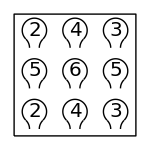

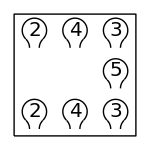

1

2

2

2

«9 more identical outputs»

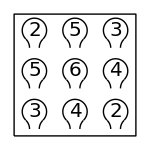

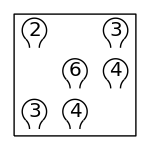

1

2

2

2

«2 more identical outputs»

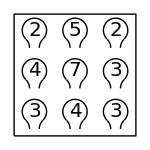

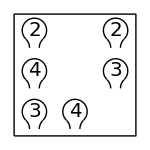

1

2

2

2

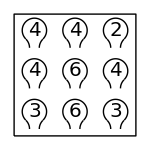

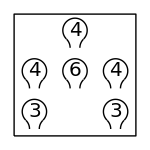

1

2

1

2

2

2

«6 more identical outputs»

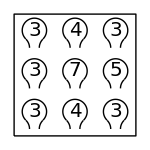

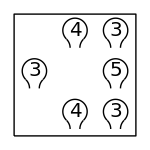

1

2

2

1

2

2

2

«7 more identical outputs»

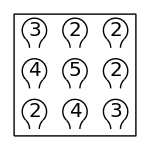

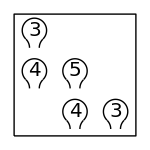

1

2

2

2

«2 more identical outputs»

1

2

2

2

«1 more identical outputs»

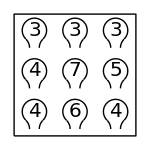

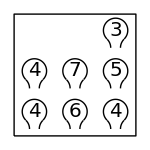

1

2

2

2

1

2

2

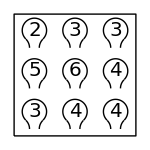

-Graphics-

1

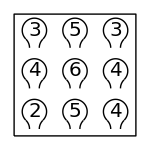

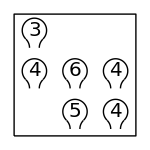

1

2

2

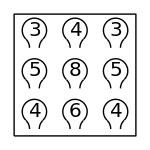

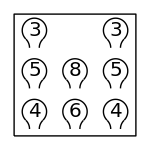

1

$Aborted

```mathematica
While[0==0,AA=RandomInteger[{0,1},{width,depth}];B=Table[cc=Total[Flatten[AA⟦(Range[i-1,i+1])∩(Range[1,width]),(Range[j-1,j+1])∩(Range[1,depth])⟧]];If[AA⟦i,j⟧==1,cc,dd=cc+2 RandomInteger[{0,1}]-1;If[dd==0,2,If[dd==-1,1,dd]]],{i,1,width},{j,1,depth}];ct=0;For[x=1,x≤2^(width depth)-1&&ct<2,x++,If[correct[A⟦x⟧,B],ct++;z=x]];If[ct==1&&Total[Flatten[A⟦z⟧]]>4,pic];Print[ct]];
```

## 4x4

## 4x5

$Aborted